```mathematica
n=1000; m=10000;
```

```mathematica
(*En este codigo, se leen los datos exportados, se hace el grafo t, y la contraparte aleatoria r. Se analizan la distribucion de grados (comun a ambos), el numero de CCs y el tamaño de las mismas. Posteriormente se corrige el hecho de los nodos sin vecinos, al añadirle {1} por cada nodo faltante en las listas de CC, y agregarle un {0} en la lista de vertex degree. Posteriormente se exporta a 'lvd'  (list of vertex degree) la lista de valores que tiene la red para los grados de los nodos, lo mismo se hace para lncct 'list of number of Connected Components' y lscct 'list of sizes of connected components'. Se generan las contrapartes aleatorias y se analizan sus propiedades, diferenciandose de las redes de parentesco acá en que sus elementos terminan en -r en vez de -t por ejemplo lsccr, lnccr. *)
```

```mathematica
(*Calculo de triangulos*)
```

```mathematica
InvertEdge[x_]:=ToExpression[ StringJoin[StringSplit[ToString[x], "<->"][[2]],"<->",StringSplit[ToString[x], "<->"][[1]]]];  Triangles=ConstantArray[0, 4];  path="D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\n2000.txt"; Do[kaux={}; colors={};    {spression=ToExpression[StringSplit[ReadLine[path]]]; While[spression≠ {0,0, 0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine[path]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], colors=Table[kaux[[i,3]], {i,1,Length[kaux]}], cycles=FindCycle[t, {3}, All], For[i= 1, i≤ Length[cycles], i++, {c=0, For[j=1, j≤Length[cycles[[i]]], j++, {edge=cycles[[i, j]], If[MemberQ[t, edge]==False, {edge=InvertEdge[edge]}], c+=colors[[Flatten[Position[t,edge]][[1]]]]}], Triangles[[c+1]]+=1}]} , m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
TableForm[Triangles]
```

415209
0
1249749
447

```mathematica
Print[Total[Triangles]]
```

1665405

```mathematica
Triangles=Triangles/Total[Triangles]; TableForm[N[Triangles]]
```

0.249314
0.
0.750417
0.000268403

```mathematica
(*Representacion de edges*)
```

```mathematica
n=100; m=1;
```

```mathematica
InvertEdge[x_]:=ToExpression[ StringJoin[StringSplit[ToString[x], "<->"][[2]],"<->",StringSplit[ToString[x], "<->"][[1]]]];  Triangles=ConstantArray[0, 4];  path="D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\n0067.txt"; Do[kaux={}; colors={};    {spression=ToExpression[StringSplit[ReadLine[path]]]; While[spression≠ {0,0, 0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine[path]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], colors=Table[kaux[[i,3]], {i,1,Length[kaux]}], cycles=FindCycle[t, {3}, All], For[i= 1, i≤ Length[cycles], i++, {c=0, For[j=1, j≤Length[cycles[[i]]], j++, {edge=cycles[[i, j]], If[MemberQ[t, edge]==False, {edge=InvertEdge[edge]}], c+=colors[[Flatten[Position[t,edge]][[1]]]]}], Triangles[[c+1]]+=1}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},6*n]} , m];
```

```mathematica
RGBColor[0,0.5,0]
```

RGBColor[0, 0.5, 0]

```mathematica
(*quedarnos con el grafico 3*)
```

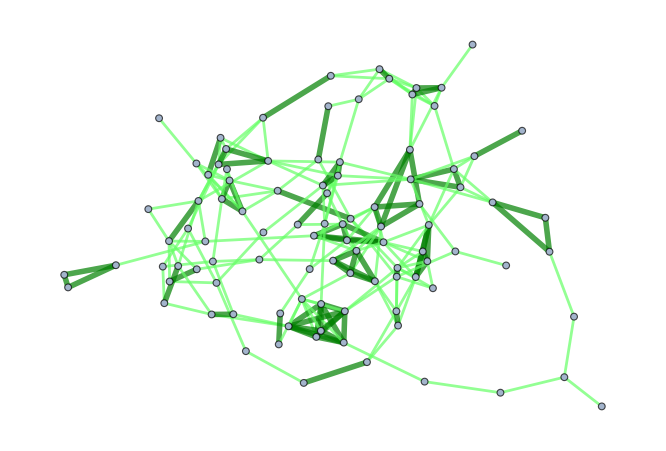

```mathematica
(*Paso auxiliar para los colores en el grafo*)
vect={}; Do[{If[colors[[i]]==1,vect=Join[vect, {{0.4,1,0.4}}]], If[colors[[i]]==0,vect=Join[vect, {{0,0.5,0}}]]}, {i,1,Length[colors]}]
(*Red de parentesco con dos colores, rojo para cuñados y verde para hermanos*)
T=Graph[t, EdgeStyle->Flatten[Table[t[[i]]->{RGBColor[vect[[i]]],Thickness[0.03*((1-colors[[i]])*0.1+0.1)]}, {i, 1, Length[t]}]]]
```

```mathematica
Graph[r]
```

-Graphics-

```mathematica
(*Muestra los triangulos en el grafo, una imagen por triangulo asi que es bastante largo*)
```

```mathematica
Table[HighlightGraph[t, cycles[[i]]], {i, 1, Length[cycles]}]
```

```mathematica
cycles
```

{{15<->14,14<->12,12<->15},{11<->14,14<->15,15<->11},{11<->15,15<->12,12<->11},{11<->14,14<->12,12<->11},{1<->11,11<->9,9<->1},{1<->8,8<->9,9<->1},{3<->7,7<->16,16<->3},{0<->19,19<->4,4<->0}}

```mathematica
TableForm[Triangles]
```

1063936
0
3200296
1723

```mathematica
Print[Total[Triangles]]
```

4265955

```mathematica
Triangles=Triangles/Total[Triangles]; TableForm[N[Triangles]]
```

0.249402
0.
0.750195
0.000403895

```mathematica
{{□}, {0.}, {0.7526078799249531}, {0.00014071294559099437}}
```

```mathematica
{{0.24865703944177023}, {0.}, {0.24865703944177023}, {0.0004985260644053883}}
```

```mathematica
PieChart[Triangles, ChartLabels->{"hhh", "hhc", "hcc", "ccc"}]
```

-Graphics-

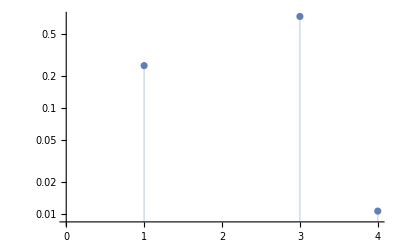

0.205128
0.
0.769231
0.025641

```mathematica
ListPlot[Triangles, ScalingFunctions->"Log", Filling->Axis]
```

```mathematica
c
```

2

```mathematica
Total[Triangles]
```

42

```mathematica
Length[cycles]
```

14

```mathematica
edge=cycles[[1, 3]]
```

16<->6

```mathematica
cycles[[1]]
```

{6<->17,17<->16,16<->6}

```mathematica
MemberQ[t, edge]
```

False

```mathematica
colors[[Flatten[Position[t,edge]][[1]]]]
```

1

{13 , 3}

```mathematica
L=StringSplit[estrin,"<->" ]
```

{6 , 17}

```mathematica
p=Position[t,1<->2]
```

{{3}}

```mathematica
t[[3]]
```

1<->2

```mathematica
p1=Flatten[p]
```

{3}

```mathematica
p1[[1]]
```

3

```mathematica
colors[[Flatten[Position[t,1<->2]][[1]]]]
```

1

```mathematica
cycles
```

{{6<->17,17<->16,16<->6},{3<->13,13<->14,14<->3},{13<->3,3<->17,17<->13},{11<->15,15<->12,12<->11},{17<->3,3<->7,7<->17},{17<->16,16<->7,7<->17},{5<->19,19<->2,2<->5},{5<->1,1<->2,2<->5},{10<->15,15<->9,9<->10},{1<->2,2<->5,5<->1},{19<->11,11<->7,7<->19},{19<->3,3<->7,7<->19},{1<->5,5<->2,2<->1},{0<->4,4<->12,12<->0}}

```mathematica
Length[cycles]
```

16

```mathematica
InvertEdge[1<->2]
```

2<->1

```mathematica
edge
```

16<->6

```mathematica
edge1=InvertEdge[edge]
```

{6<->16}

```mathematica
InvertEdge[11]
```

121

```mathematica
StringJoin[L[[2]],"<->",L[[1]]]
```

3<->13